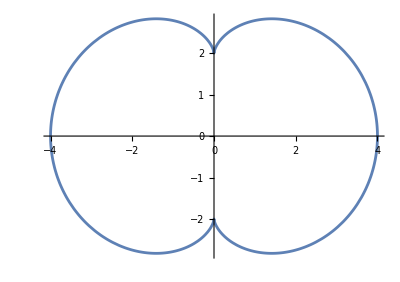

```mathematica
(**Question 1 **)
ParametricPlot[{3 Cos[ϕ]+Cos[3 ϕ],3 Sin[ϕ]+Sin[3 ϕ]},{ϕ,0,2 π}]
```

```mathematica
x[ϕ_]= 3 Cos[ϕ]+Cos[3 ϕ]
y[ϕ_]= 3 Sin[ϕ]+Sin[3 ϕ]
dx[ϕ_] = x'[ϕ]
dy[ϕ_]= y'[ϕ]
ddx[ϕ_]= dx'[ϕ]
ddy[ϕ_]= dy'[ϕ]
```

3 Cos[ϕ]+Cos[3 ϕ]

3 Sin[ϕ]+Sin[3 ϕ]

-3 Sin[ϕ]-3 Sin[3 ϕ]

3 Cos[ϕ]+3 Cos[3 ϕ]

-3 Cos[ϕ]-9 Cos[3 ϕ]

-3 Sin[ϕ]-9 Sin[3 ϕ]

```mathematica
upper[ϕ_]= dx[ϕ]^2 + dy[ϕ]^2
lower[ϕ_]= dx[ϕ]ddy[ϕ] - ddx[ϕ]dy[ϕ]
p[ϕ_]= upper[ϕ] / lower[ϕ]
```

(3 Cos[ϕ]+3 Cos[3 ϕ])^2+(-3 Sin[ϕ]-3 Sin[3 ϕ])^2

-((-3 Cos[ϕ]-9 Cos[3 ϕ]) (3 Cos[ϕ]+3 Cos[3 ϕ]))+(-3 Sin[ϕ]-9 Sin[3 ϕ]) (-3 Sin[ϕ]-3 Sin[3 ϕ])

((3 Cos[ϕ]+3 Cos[3 ϕ])^2+(-3 Sin[ϕ]-3 Sin[3 ϕ])^2)/(-((-3 Cos[ϕ]-9 Cos[3 ϕ]) (3 Cos[ϕ]+3 Cos[3 ϕ]))+(-3 Sin[ϕ]-9 Sin[3 ϕ]) (-3 Sin[ϕ]-3 Sin[3 ϕ]))

```mathematica
FullSimplify[p[ϕ]]
```

1/2

```mathematica
FullSimplify[upper[ϕ]]
FullSimplify[lower[ϕ]]
```

36 Cos[ϕ]^2

72 Cos[ϕ]^2

```mathematica
Ex[ϕ_]= x[ϕ] + p[ϕ]* -dy[ϕ]
Ey[ϕ_]= y[ϕ] + p[ϕ]* dx[ϕ]
FullSimplify[Ex[ϕ]]
FullSimplify[Ey[ϕ]]
```

3 Cos[ϕ]+Cos[3 ϕ]+((-3 Cos[ϕ]-3 Cos[3 ϕ]) ((3 Cos[ϕ]+3 Cos[3 ϕ])^2+(-3 Sin[ϕ]-3 Sin[3 ϕ])^2))/(-((-3 Cos[ϕ]-9 Cos[3 ϕ]) (3 Cos[ϕ]+3 Cos[3 ϕ]))+(-3 Sin[ϕ]-9 Sin[3 ϕ]) (-3 Sin[ϕ]-3 Sin[3 ϕ]))

3 Sin[ϕ]+(((3 Cos[ϕ]+3 Cos[3 ϕ])^2+(-3 Sin[ϕ]-3 Sin[3 ϕ])^2) (-3 Sin[ϕ]-3 Sin[3 ϕ]))/(-((-3 Cos[ϕ]-9 Cos[3 ϕ]) (3 Cos[ϕ]+3 Cos[3 ϕ]))+(-3 Sin[ϕ]-9 Sin[3 ϕ]) (-3 Sin[ϕ]-3 Sin[3 ϕ]))+Sin[3 ϕ]

-Cos[ϕ] (-2+Cos[2 ϕ])

2 Sin[ϕ]^3

Question 1b

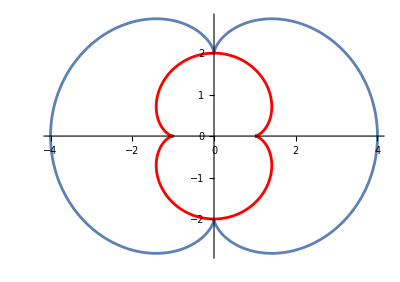

```mathematica
Show[ParametricPlot[{3 Cos[ϕ]+Cos[3 ϕ],3 Sin[ϕ]+Sin[3 ϕ]},{ϕ,0,2 π}],ParametricPlot[{-Cos[ϕ] (-2+Cos[2 ϕ]),2 Sin[ϕ]^3},{ϕ,0,2 π},PlotStyle->Red]]
```

Evolute of a curve consists of singular points of the wave fronts

```mathematica
nx[ϕ_]= -dy[ϕ]
ny[ϕ_]= dx[ϕ]
FullSimplify[gammax[ϕ_, α_]= x[ϕ] + α * nx[ϕ]]
FullSimplify[gammay[ϕ_, α_]= y[ϕ] + α * ny[ϕ]]
```

-3 Cos[ϕ]-3 Cos[3 ϕ]

-3 Sin[ϕ]-3 Sin[3 ϕ]

2 Cos[ϕ] (1+(1-3 α) Cos[2 ϕ])

-3 (-1+α) Sin[ϕ]+(1-3 α) Sin[3 ϕ]

```mathematica
Manipulate[
Show[
ParametricPlot[{3 Cos[ϕ]+Cos[3 ϕ],3 Sin[ϕ]+Sin[3 ϕ]},{ϕ,0,2 π}, PlotStyle-> Orange],
ParametricPlot[{-Cos[ϕ] (-2+Cos[2 ϕ]),2 Sin[ϕ]^3},{ϕ,0,2 π},PlotStyle->Red],
ParametricPlot[{gammax[ϕ, α], gammay[ϕ, α]},{ϕ,0,2 π}], 
PlotLabel->Row[{"α = ",α}]
],{α,-9,9,0.1}
]
```

Explanation: The Huygens’ principle states that the evolute of a curve consists of singular points of the wave fronts , which, as seen in the plot, when  is exactly the shape of our evolute. This principle is illustrated by observing that as we vary α, the parameter controlling the distance of the wavefronts from the evolute, the wavefronts smoothly envelop the evolute curve. At α = 0.5, the wavefronts are precisely tangent to the evolute, indicating that the evolute curve indeed comprises the singular points of the wavefronts. This demonstrates how Huygens’s principle captures the behavior of wave propagation by associating each point on a wavefront with the corresponding normal direction to the curve, resulting in the formation of the evolute.
Singular points: We can find singularity points by checking which value of  makes both derivatives 0

```mathematica
FullSimplify[dx[ϕ]]
FullSimplify[dy[ϕ]]
```

-12 Cos[ϕ]^2 Sin[ϕ]

3 (Cos[ϕ]+Cos[3 ϕ])

The result is anything that makes a cosine = 0, so there are multiple singularity points, however, since we limit , these are limited to

```mathematica
FullSimplify[-3 Sin[Pi/2]-3 Sin[3Pi/2]]
FullSimplify[3 Cos[Pi/2]+3Cos[3Pi/2]]
```

0

0

```mathematica
FullSimplify[dx[ϕ]^2 + dy[ϕ]^2]
```

36 Cos[ϕ]^2